```mathematica
f[x_]= x* E^(-x^2)+x^2/3-x^3
```

ⅇ^(-x^2) x+x^2/3-x^3

```mathematica
Plot[f'[x],{x,-7,8}]
```

-Graphics-

```mathematica
Solve[f'[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(x^2)+(2 x)/3-3 x^2+2 ⅇ^(x^2) x^2==0,x]

```mathematica
FindRoot[f[x],{x,-6}]
```

```mathematica
f'''''[0]
```

60

```mathematica
Limit [f[x], x-> 7]
```

-980/3+7 ⅇ^49

```mathematica
N[%]
```

NLimit[2.71828^(x^2) x+0.333333 x^2-1. x^3,x→7.]

```mathematica
Limit [f[x], x-> 6]
```

6 (-34+ⅇ^36)

```mathematica
N[%]
```

2.58674×10^16

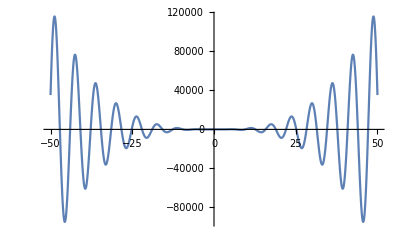

```mathematica
Plot[x^2Cos[x]-x^3Sin[x],{x,-50,50}]
```

```mathematica
h[x_]= x^2Cos[x]-x^3Sin[x]
```

x^2 Cos[x]-x^3 Sin[x]

```mathematica
h[-1]
```

Cos[1]-Sin[1]

```mathematica
h[1]
```

Cos[1]-Sin[1]

```mathematica
g[x_]=x^2Sin[x]-x^3Cos[x]
```

-x^3 Cos[x]+x^2 Sin[x]

```mathematica
g[1]
```

-Cos[1]+Sin[1]

```mathematica
g[-1]
```

Cos[1]-Sin[1]

```mathematica
Cos[1]-Sin[1]
-g[1]
```

Cos[1]-Sin[1]

Cos[1]-Sin[1]

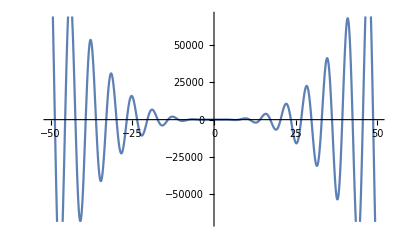

```mathematica
Plot[g[x],{x,-50,50}]
```

```mathematica
g[1]
```

-Cos[1]+Sin[1]

```mathematica
g[-1]
```

Cos[1]-Sin[1]

```mathematica
-g[1]
```

Cos[1]-Sin[1]

```mathematica
a[x_]= (x^2+x^3)Tan[x]
```

(x^2+x^3) Tan[x]

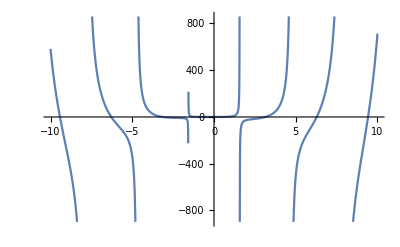

```mathematica
Plot[a[x],{x,-10,10}]
```

```mathematica
a[3]
```

36 Tan[3]

```mathematica
a[-3]
```

18 Tan[3]

```mathematica
-a[3]
```

-36 Tan[3]

```mathematica
p[x_]=ArcTan[x^2-3x]
```

-ArcTan[3 x-x^2]

```mathematica
-ArcTan[3 x-x^2]
p'[x]
```

-ArcTan[3 x-x^2]

-(3-2 x)/(1+(3 x-x^2)^2)

-(3-2 x)/(1+(3 x-x^2)^2)

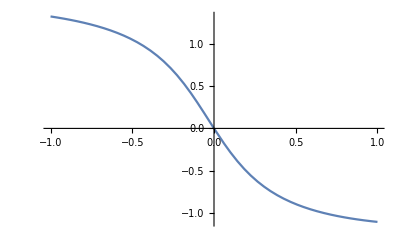

```mathematica
Plot[-ArcTan[3 x-x^2],{x,-1,1}]
```

```mathematica
Solve[c'[x]==0,x,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[c'[x]==0,x,Reals]

```mathematica
FindRoot[c'[x],{x,0}]
```

FindRoot::nlnum: The function value {c'[0.]} is not a list of numbers with dimensions {1} at {x} = {0.}.

FindRoot[c'[x],{x,0}]

```mathematica
c'[x]
```

c'[x]

```mathematica
p'[x]
```

-(3-2 x)/(1+(3 x-x^2)^2)

```mathematica
Solve[p'[x]==0,x]
```

{{x→3/2}}

```mathematica
p[3/2]
```

-ArcTan[9/4]

```mathematica
N[%]
```

-1.15257

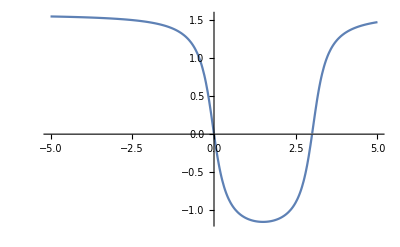

```mathematica
Plot[p[x],{x,-5,5}]
```

```mathematica
Solve[p[x]==0,x]
```

{{x→0},{x→3}}

```mathematica
o[x_]=3x^5+5x^3-14x-14
```

-14-14 x+5 x^3+3 x^5

```mathematica
i[x_]= 3x^5-37x^3-25x^2-6
```

-6-25 x^2-37 x^3+3 x^5

```mathematica
NSolve[o[x]==i[x],x]
```

{{}}

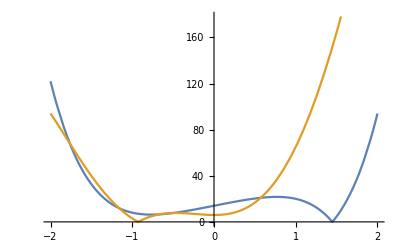

```mathematica
Plot[{Abs[o[x]],Abs[i[x]]},{x,-2,2}]
```

```mathematica
Solve[3x^5+5x^3-14x-14==3x^5-37x^3-25x^2-6,x]
```

{{x→-2/3},{x→-1/2},{x→4/7}}

```mathematica
Inte
```

```mathematica
Integrate[Abs[Abs[o[x]]-Abs[i[x]]],{-2/3,4/7}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {-2/3,4/7}.

Integrate[0,{-2/3,4/7}]

```mathematica
Integrate[Abs[3x^5+5x^3-14x-14]-Abs[(3x^5-37x^3-25x^2-6)],{x,-2/3,4/7}]
```

166972/27783

```mathematica
N[%]
```

6.00986

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```

```mathematica
y[x_]=Log[x]/(1+x^2)
```

Log[x]/(1+x^2)

```mathematica
Simpson[y,{1,3,50}]
```

0.23311245616192170808

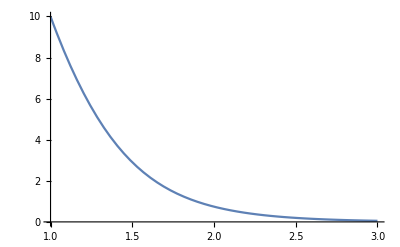

```mathematica
Plot[Abs[y''''[x]],{x,1,3}]
```

```mathematica
2^5/(180*50^4)*11
```

11/35156250

```mathematica
N[%]
```

3.12889×10^-7

```mathematica
f[x]
```

ⅇ^(x^2) x+x^2/3-x^3

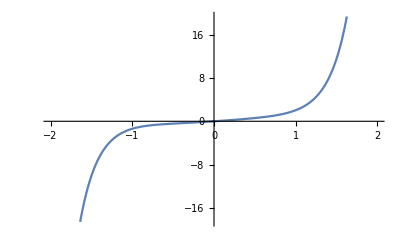

```mathematica
Plot[{f[x],},{x,-2,2}]
```

```mathematica
f'[x]
```

ⅇ^(x^2)+(2 x)/3-3 x^2+2 ⅇ^(x^2) x^2

```mathematica
NSolve[f'[x]==0,x,Reals]
```

{}

```mathematica
p[x_]=ArcTan[x^2-3x]
```

-ArcTan[3 x-x^2]

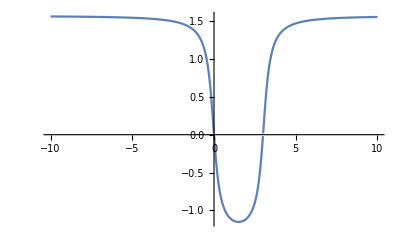

```mathematica
Plot[p[x],{x,-10,10}]
```

```mathematica
Solve[p[x]==0,x]
```

{{x→0},{x→3}}

```mathematica
Solve[f'[x]==0,x,Reals]
```

```mathematica
f'[x]
```

ⅇ^(x^2)+(2 x)/3-3 x^2+2 ⅇ^(x^2) x^2

```mathematica
NSolve[f'[x]==0,x,Reals]
```

{{x→-0.364792},{x→0.493599}}

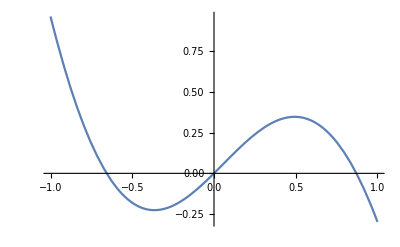

```mathematica
Plot [{f[x]},{x,-1,1}]
```

```mathematica
f'''''[0]
```

60